```mathematica
us[a_,b_] := a+b
```

```mathematica
vs[a_,b_] := b/(a+b)^2
```

```mathematica
Det[{{-d11/Lx^2kx^2 π^2-d11/Ly^2ky^2 π^2-1- 4 us[a,b] vs[a,b]+6us[a,b]vs[a,b]Exp[-τ λ] -λ,-2us[a,b]^2+3us[a,b]^2Exp[-τ λ]},{-2us[a,b]vs[a,b],-d22 kx^2 π^2/Lx^2-d22 ky^2 π^2/Ly^2-us[a,b]^2-λ}}];
```

```mathematica
char[a_,b_,d11_,d22_, τ_, Lx_,Ly_, kx_, ky_, λ_]:=a^2+2 a b+b^2+(a^2 d11 kx^2 π^2)/Lx^2+(2 a b d11 kx^2 π^2)/Lx^2+(b^2 d11 kx^2 π^2)/Lx^2+(d22 kx^2 π^2)/Lx^2+(4 a b d22 kx^2 π^2)/((a+b^2) Lx^2)+(4 b^2 d22 kx^2 π^2)/((a+b^2) Lx^2)-(6 a b d22 ⅇ^(-λ τ) kx^2 π^2)/((a+b^2) Lx^2)-(6 b^2 d22 ⅇ^(-λ τ) kx^2 π^2)/((a+b^2) Lx^2)+(a^2 d11 ky^2 π^2)/Ly^2+(2 a b d11 ky^2 π^2)/Ly^2+(b^2 d11 ky^2 π^2)/Ly^2+(d22 ky^2 π^2)/Ly^2+(4 a b d22 ky^2 π^2)/((a+b^2) Ly^2)+(4 b^2 d22 ky^2 π^2)/((a+b^2) Ly^2)-(6 a b d22 ⅇ^(-λ τ) ky^2 π^2)/((a+b^2) Ly^2)-(6 b^2 d22 ⅇ^(-λ τ) ky^2 π^2)/((a+b^2) Ly^2)+(d11 d22 kx^4 π^4)/Lx^4+(d11 d22 ky^4 π^4)/Ly^4+(2 d11 d22 kx^2 ky^2 π^4)/(Lx^2 Ly^2)+λ+a^2 λ+2 a b λ+b^2 λ+(4 a b λ)/(a+b^2)+(4 b^2 λ)/(a+b^2)-(6 a b ⅇ^(-λ τ) λ)/(a+b^2)-(6 b^2 ⅇ^(-λ τ) λ)/(a+b^2)+(d11 kx^2 π^2 λ)/Lx^2+(d22 kx^2 π^2 λ)/Lx^2+(d11 ky^2 π^2 λ)/Ly^2+(d22 ky^2 π^2 λ)/Ly^2+λ^2
```

```mathematica
bif=0.313
```

```mathematica
Manipulate[
Show[
Plot[0.33/Max[Re[Flatten[Table[NSolveValues[char[a,b,d11,d22,τ,Lx,Ly,kx,ky,λ]==0&&-10<=Re[λ]<=10&&-ImRange<=Im[λ]<=ImRange,λ],{kx,0,K},{ky,0,K}]]]],{Lx,0.32,1},PlotRange->{{0,1},{0,12}}],
Graphics[{Orange,Dashed,Line[{{bif,0},{bif,12}}]}],Axes->False,PlotTheme->"BoldLabels",LabelStyle->Directive[FontFamily->"Times New Roman",Bold,FontSize->12],Frame->{True,True,True,True},FrameLabel->{Style["Lx",20,Bold],Style["time",20,Bold]},FrameStyle->Directive[Black, Thick, 15],FrameTicks->{{{0,2,4,6,8,10,12},None},{{0.2,0.4,0.6,0.8,1.0},None}}
],
{{a,0.1},0.001,5},{{b,1.5},0.001,5},{{d11,0.01},0.001,5},{{d22,1},0.001,5},{{τ,0.0},0,10},{{Ly,0.1},0.001,5},{{K,3},0,15,1},{{ImRange,10},0.1,50}]
```

```mathematica
bif=0.382088
```

```mathematica
Manipulate[
Show[
Plot[0.33/Max[Re[Flatten[Table[NSolveValues[char[a,b,d11,d22,τ,Lx,Ly,kx,ky,λ]==0&&-10<=Re[λ]<=10&&-ImRange<=Im[λ]<=ImRange,λ],{kx,0,K},{ky,0,K}]]]],{Lx,0.337,3},PlotRange->{{0,1},{0,12}}],
Graphics[{Orange,Dashed,Line[{{bif,0},{bif,12}}]}],Axes->False,PlotTheme->"BoldLabels",LabelStyle->Directive[FontFamily->"Times New Roman",Bold,FontSize->12],Frame->{True,True,True,True},FrameLabel->{Style["Lx",20,Bold],Style["time",20,Bold]},FrameStyle->Directive[Black, Thick, 15],FrameTicks->{{{0,2,4,6,8,10,12},None},{{0.2,0.4,0.6,0.8,1.0},None}}
],
{{a,0.1},0.001,5},{{b,0.9},0.001,5},{{d11,0.01},0.001,5},{{d22,0.2},0.001,5},{{τ,0.0},0,10},{{Ly,0.1},0.001,5},{{K,3},0,15,1},{{ImRange,10},0.1,50}]
```

```mathematica
Manipulate[
Show[
Plot[0.33/Max[Re[Flatten[Table[NSolveValues[char[a,b,d11,d22,τ,Lx,Ly,kx,ky,λ]==0&&-10<=Re[λ]<=10&&-ImRange<=Im[λ]<=ImRange,λ],{kx,0,K},{ky,0,K}]]]],{Lx,0.337,3},PlotRange->{{0,1},{0,12}}],
Graphics[{Orange,Dashed,Line[{{bif,0},{bif,12}}]}],Axes->False,PlotTheme->"BoldLabels",LabelStyle->Directive[FontFamily->"Times New Roman",Bold,FontSize->12],Frame->{True,True,True,True},FrameLabel->{Style["Lx",20,Bold],Style["time",20,Bold]},FrameStyle->Directive[Black, Thick, 15],FrameTicks->{{{0,2,4,6,8,10,12},None},{{0.2,0.4,0.6,0.8,1.0},None}}
],
{{a,0.1},0.001,5},{{b,0.9},0.001,5},{{d11,0.01},0.001,5},{{d22,0.2},0.001,5},{{τ,0.2},0,10},{{Ly,0.1},0.001,5},{{K,3},0,15,1},{{ImRange,10},0.1,50}]
```

```mathematica
Manipulate[
Show[
Plot[0.33/Max[Re[Flatten[Table[NSolveValues[char[a,b,d11,d22,0,Lx,Ly,kx,ky,λ]==0&&-10<=Re[λ]<=10&&-ImRange<=Im[λ]<=ImRange,λ],{kx,0,K},{ky,0,K}]]]],{Lx,0.34,3},PlotRange->{{0,1},{0,12}}, PlotStyle-> Red],
Plot[0.33/Max[Re[Flatten[Table[NSolveValues[char[a,b,d11,d22,0.2,Lx,Ly,kx,ky,λ]==0&&-10<=Re[λ]<=10&&-ImRange<=Im[λ]<=ImRange,λ],{kx,0,K},{ky,0,K}]]]],{Lx,0.34,3},PlotRange->{{0,1},{0,12}}, PlotStyle-> Green],
Plot[0.33/Max[Re[Flatten[Table[NSolveValues[char[a,b,d11,d22,0.5,Lx,Ly,kx,ky,λ]==0&&-10<=Re[λ]<=10&&-ImRange<=Im[λ]<=ImRange,λ],{kx,0,K},{ky,0,K}]]]],{Lx,0.34,3},PlotRange->{{0,1},{0,12}}, PlotStyle-> Black],
Graphics[{Orange,Dashed,Line[{{bif,0},{bif,12}}]}],Axes->False,PlotTheme->"BoldLabels",LabelStyle->Directive[FontFamily->"Times New Roman",Bold,FontSize->12],Frame->{True,True,True,True},FrameLabel->{Style["Lx",20,Bold],Style["time",20,Bold]},FrameStyle->Directive[Black, Thick, 15],FrameTicks->{{{0,2,4,6,8,10,12},None},{{0.2,0.4,0.6,0.8,1.0},None}}
],
{{a,0.1},0.001,5},{{b,0.9},0.001,5},{{d11,0.01},0.001,5},{{d22,0.2},0.001,5},{{Ly,0.1},0.001,5},{{K,3},0,15,1},{{ImRange,10},0.1,50}]
```

```mathematica
Manipulate[
Show[
Plot[Log[2]/Max[Re[Flatten[Table[NSolveValues[char[a,b,d11,d22,0,Lx,Ly,kx,ky,λ]==0&&-10<=Re[λ]<=10&&-ImRange<=Im[λ]<=ImRange,λ],{kx,0,K},{ky,0,K}]]]],{Lx,0.34,3},PlotRange->{{0,1},{0,40}}, PlotStyle-> Red],
Plot[Log[2]/Max[Re[Flatten[Table[NSolveValues[char[a,b,d11,d22,0.5,Lx,Ly,kx,ky,λ]==0&&-10<=Re[λ]<=10&&-ImRange<=Im[λ]<=ImRange,λ],{kx,0,K},{ky,0,K}]]]],{Lx,0.34,3},PlotRange->{{0,1},{0,40}}, PlotStyle-> Green],
Plot[Log[2]/Max[Re[Flatten[Table[NSolveValues[char[a,b,d11,d22,1,Lx,Ly,kx,ky,λ]==0&&-10<=Re[λ]<=10&&-ImRange<=Im[λ]<=ImRange,λ],{kx,0,K},{ky,0,K}]]]],{Lx,0.34,3},PlotRange->{{0,1},{0,40}}, PlotStyle-> Black],
Graphics[{Orange,Dashed,Line[{{bif,0},{bif,12}}]}],Axes->False,PlotTheme->"BoldLabels",LabelStyle->Directive[FontFamily->"Times New Roman",Bold,FontSize->12],Frame->{True,True,True,True},FrameLabel->{Style["Lx",20,Bold],Style["time",20,Bold]},FrameStyle->Directive[Black, Thick, 15]
],
{{a,0.1},0.001,5},{{b,0.9},0.001,5},{{d11,0.01},0.001,5},{{d22,0.2},0.001,5},{{Ly,0.1},0.001,5},{{K,3},0,15,1},{{ImRange,10},0.1,50}]
```

```mathematica
Manipulate[
Show[
Plot[0.9/Max[Re[Flatten[Table[NSolveValues[char[a,b,d11,d22,0,Lx,Ly,kx,ky,λ]==0&&-10<=Re[λ]<=10&&-ImRange<=Im[λ]<=ImRange,λ],{kx,0,K},{ky,0,K}]]]],{Lx,0.34,3},PlotRange->{{0,1},{0,12}}, PlotStyle-> Red],
Plot[0.9/Max[Re[Flatten[Table[NSolveValues[char[a,b,d11,d22,0.2,Lx,Ly,kx,ky,λ]==0&&-10<=Re[λ]<=10&&-ImRange<=Im[λ]<=ImRange,λ],{kx,0,K},{ky,0,K}]]]],{Lx,0.34,3},PlotRange->{{0,1},{0,12}}, PlotStyle-> Green],
Plot[0.9/Max[Re[Flatten[Table[NSolveValues[char[a,b,d11,d22,0.5,Lx,Ly,kx,ky,λ]==0&&-10<=Re[λ]<=10&&-ImRange<=Im[λ]<=ImRange,λ],{kx,0,K},{ky,0,K}]]]],{Lx,0.34,3},PlotRange->{{0,1},{0,12}}, PlotStyle-> Black],
Graphics[{Orange,Dashed,Line[{{bif,0},{bif,12}}]}],Axes->False,PlotTheme->"BoldLabels",LabelStyle->Directive[FontFamily->"Times New Roman",Bold,FontSize->12],Frame->{True,True,True,True},FrameLabel->{Style["Lx",20,Bold],Style["time",20,Bold]},FrameStyle->Directive[Black, Thick, 15],FrameTicks->{{{0,2,4,6,8,10,12},None},{{0.2,0.4,0.6,0.8,1.0},None}}
],
{{a,0.1},0.001,5},{{b,0.9},0.001,5},{{d11,0.01},0.001,5},{{d22,0.2},0.001,5},{{Ly,0.1},0.001,5},{{K,3},0,15,1},{{ImRange,10},0.1,50}]
```

```mathematica
Manipulate[
Show[
Plot[Log[2]/Max[Re[Flatten[Table[NSolveValues[char[a,b,d11,d22,0,Lx,Ly,kx,ky,λ]==0&&-10<=Re[λ]<=10&&-ImRange<=Im[λ]<=ImRange,λ],{kx,0,K},{ky,0,K}]]]],{Lx,0.34,3},PlotRange->{{0,1},{0,40}}, PlotStyle-> Red],
Plot[Log[2]/Max[Re[Flatten[Table[NSolveValues[char[a,b,d11,d22,0.5,Lx,Ly,kx,ky,λ]==0&&-10<=Re[λ]<=10&&-ImRange<=Im[λ]<=ImRange,λ],{kx,0,K},{ky,0,K}]]]],{Lx,0.34,3},PlotRange->{{0,1},{0,40}}, PlotStyle-> Green],
Plot[Log[2]/Max[Re[Flatten[Table[NSolveValues[char[a,b,d11,d22,1,Lx,Ly,kx,ky,λ]==0&&-10<=Re[λ]<=10&&-ImRange<=Im[λ]<=ImRange,λ],{kx,0,K},{ky,0,K}]]]],{Lx,0.34,3},PlotRange->{{0,1},{0,40}}, PlotStyle-> Black],
Graphics[{Orange,Dashed,Line[{{bif,0},{bif,12}}]}],Axes->False,PlotTheme->"BoldLabels",LabelStyle->Directive[FontFamily->"Times New Roman",Bold,FontSize->12],Frame->{True,True,True,True},FrameLabel->{Style["Lx",20,Bold],Style["time",20,Bold]},FrameStyle->Directive[Black, Thick, 15]
],
{{a,0.1},0.001,5},{{b,1.5},0.001,5},{{d11,0.01},0.001,5},{{d22,0.2},0.001,5},{{Ly,0.1},0.001,5},{{K,3},0,15,1},{{ImRange,10},0.1,50}]
```

```mathematica
f=OpenRead["D:\\Delay_Reaction_Diffusion_SM\\Simulation_python\\TTP_lx_random_initial\\Sheet1.txt"]
data = ReadList[f,{Number,Number}];
Close[f]
```

InputStream[…]

D:\Delay_Reaction_Diffusion_SM\Simulation_python\TTP_lx_random_initial\Sheet1.txt

```mathematica
bif=0.382088
```

0.382088

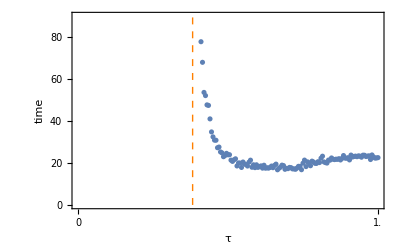

```mathematica
Show[ListPlot[data,Frame->True, PlotRange->{{0,1}, {0,90}}],Graphics[{Orange,Dashed,Line[{{bif,0},{bif,90}}]}],Axes->False,PlotTheme->"BoldLabels",LabelStyle->Directive[FontFamily->"Times New Roman",Bold,FontSize->12],Frame->{True,True,True,True},FrameLabel->{Style["τ",20,Bold],Style["time",20,Bold]},FrameStyle->Directive[Black, Thick, 15],FrameTicks->{{{0,20,40,60,80,100},None},{{0,0.5, 1.0,1.5,2,2.5, 3},None}}]
```